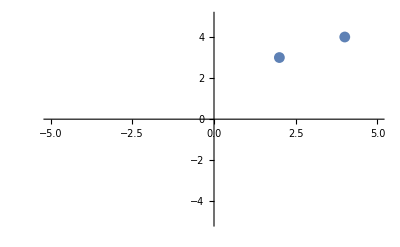

```mathematica
ListPlot[{{2, 3}, {4, 4}}, Mesh -> All, PlotRange->{{-5, 5}, {-5, 5}}]
```

```mathematica
Graphics3D@{Sphere[{0,0,0},.95],Point[CoordinateTransformData["Spherical"->"Cartesian","Mapping",#]&/@Table[{1,RandomReal[{0,Pi}],RandomReal[{-Pi,Pi}]},{200}]]}
```

-Graphics3D-

```mathematica
data = Table[{1, x * Pi / 180, y * Pi / 180}, {y, -90,  90, 90}, {x, -180, 180, 90}]
```

{{{1,-π,-π/2},{1,-π/2,-π/2},{1,0,-π/2},{1,π/2,-π/2},{1,π,-π/2}},{{1,-π,0},{1,-π/2,0},{1,0,0},{1,π/2,0},{1,π,0}},{{1,-π,π/2},{1,-π/2,π/2},{1,0,π/2},{1,π/2,π/2},{1,π,π/2}}}

```mathematica
Graphics3D[{Sphere[{0, 0, 0}, 0.95], Sphere[{0.5, 0.5, 0}, 0.95], Point[{0, 0, 1}]}]
```

-Graphics3D-

```mathematica
Graphics3D[(Point/@data)]
```

-Graphics3D-

```mathematica
FromSphericalCoordinates[{1,1,1}]
```